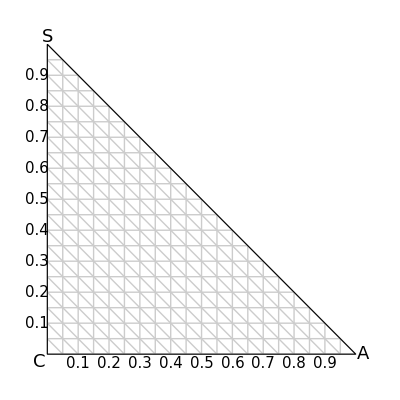

```mathematica
ternary=
Graphics[{
{Thin,GrayLevel[0.8],Table[{Line[{{0,i},{1-i,i}}],Line[{{i,0},{i,1-i}}],Line[{{0,i},{i,0}}]},{i,0,1,0.05}]},
{EdgeForm[Thick],FaceForm[None],Polygon[{{0,1},{0,0},{1,0}}]},
Table[{Text[Style[j,15],{j,-0.03}],Text[Style[j,15],{-0.035,j}]},{j,0.1,0.9,0.1}],
Text[Style["S",18],{0,1.025}],Text[Style["A",18],{1.025,0}],Text[Style["C",18],{-0.025,-0.025}]
},AspectRatio->1,ImageSize->400]
```